# Exact continuum representation of long-range interacting systems: Example 1: Interacting Skyrmions

by Andreas A. Buchheit and Torsten Keßler

The exact continuum representation for long-range interacting systems is applied to the computation of interaction energies in a dipolar 2D spin lattice with two Néel Skyrmions.

## Epstein Zeta

```mathematica
ClearAll@"Global`*";
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"epsteinZeta.m"
```

## Mathematica Settings

```mathematica
Off[Part::partd]
```

```mathematica
precision=20;
```

## Parameter Choices

Number of derivatives taken into account in the SEM operator and value of ν. For numerical reasons, choose ν∈ C∖N, where ν can be arbitrarily close to any integer number.

```mathematica
numDerivatives=2;
νFixed=3-1/1000;
```

Skyrmion domain wall width (Wang2018)

```mathematica
λ1=5;
```

Skyrmion radius in units of λ

```mathematica
R1=26/5;
```

Distance between Skyrmions in units of λ

```mathematica
s=15;
```

## Skyrmion

Skyrmion profile from X. Wang, H. Yuan,  and X. Wang, “A theory on skyrmion size,” Commun. Phys. 1, 1 (2018).

```mathematica
Θ[r_,R_,λ_]=2*ArcTan[Sinh[R]/Sinh[r/λ]];
```

```mathematica
$Assumptions={r>0,R>0,λ>0}
```

{r>0,R>0,λ>0}

```mathematica
Θ2[r_,R_,λ_]=ArcCos[2/(Pi)*Integrate[1/(1+(y-R)^2),{y,0,r/λ}]+1]//Normal;
```

Neel skyrmion in polar coordinates

```mathematica
S[r_,ϕ_,λ_]={Sin[Θ[r,R1,λ]]*Cos[ϕ],Sin[Θ[r,R1,λ]]*Sin[ϕ],Cos[Θ[r,R1,λ]]}//TrigExpand//FullSimplify;
```

Cartesian coordinates

```mathematica
Sy[y1_,y2_,λ_]=S[Sqrt[y1^2+y2^2],ArcTan[y1,y2],λ]//FullSimplify;
```

Function g describing two Skyrmions at distance s. Note that only the rotationally symmetric part of the dipole interaction needs to be taken into account as the remaining part cancels.

```mathematica
g0[x1_,x2_]={0,0,1}.(Sy[x1-s/(2*1/λ),x2,λ]+Sy[x1+s/(2*1/λ),x2,λ]-{0,0,1})/Norm[Sy[x1-s/(2*1/λ),x2,λ]+Sy[x1+s/(2*1/λ),x2,λ]-{0,0,1}]/.Abs->RealAbs//Simplify;
```

## SEM Operator

Directional derivative applied to Zg = EpsteinZeta[...]*g. The Epstein zeta derivative is computed via finite differences.

```mathematica
DirectionalDerivativeFinite[Zg_,varY_,varX_,h_]:=Sum[I*D[DifferenceQuotient[Zg,{varY[[i]],h}],varX[[i]]],{i,1,Length[varX]}];
```

Higher order directional derivatives

```mathematica
ZetaDerivativeHigher[dim_,n_,h_]:=Nest[DirectionalDerivativeFinite[#,Array[y,dim],Array[x,dim],h]&,Z@@Array[y,dim]*g1@@Array[x,dim],n]/.{y[t_]:>0};
```

SEM Operator generation with derivatives up to order order, evaluated via finite differences with discretization h. The Epstein zeta terms are collected first in order to have as few evaluations as possible.

```mathematica
GenerateSEMOperator[ALambda_,ν_,x_,a_,order_,h_]:=Collect[Sum[1/k!*ZetaDerivativeHigher[Length[x],k,h],{k,0,order}],Z[_,_]]/.Z[t1_,t2_]:>epsteinZetaReg[ν,ALambda,x-a,{t1/(2Pi),t2/(2Pi)},6,200];
```

Number of Epstein zeta evaluations

```mathematica
Variables[Sum[1/k!*ZetaDerivativeHigher[2,k,h],{k,0,4}]]//Length
```

31

```mathematica
aSq={{1,0},{0,1}};
```

Compute Epstein zeta and insert into the SEM operator

```mathematica
SEMOpGeneral=Chop[(Collect[((GenerateSEMOperator[aSq,νFixed,{0,0},{0,0},numDerivatives,10^(-13)]//Simplify)/.{x[i_]:>x[[i]]}),g1[_,_]])//Expand,10^(-13)];
```

Insert the function g and obtain the SEM operator as a function of test particle position x and wavelength λ.

```mathematica
SEMOp[x_,λ_]=(SEMOpGeneral/.g1->g0);
```

```mathematica
SEMOpEvaluatedSkyrmionEpsilon[x1_,x2_,λ_,ϵ_]=SEMOp[{x1,x2},λ]-2Pi*Sum[Pochhammer[1/2,k]/(2k)!/Pochhammer[2/2,k]*ϵ^(-(νFixed-(2k+2)))/(νFixed-(2k+2))*Nest[Laplacian[#,{x1,x2}]&,g0[x1,x2],k],{k,0,1}];
```

## Sum

Sum ∑' s(z-x) g(z)

```mathematica
sumUpper=150;
```

```mathematica
NSummandFunc[x1_?NumericQ,x2_?NumericQ,y1_?NumericQ,y2_?NumericQ,λ_?NumericQ]=N[1/Sqrt[y1^2+y2^2]^νFixed*g0[y1-x1,y2-x2],15];
```

```mathematica
SumValueSkyrmion[x1_,x2_,λ_]:=ParallelSum[If[Norm[{y1,y2}]≠0,NSummandFunc[x1,x2,y1,y2,λ],0],{y1,-sumUpper,sumUpper},{y2,-sumUpper,sumUpper}];
```

## Quadrature

```mathematica
jacobiAlgorithm::usage="computes the nodes and weights for a given set of orthogonal polynomials, specified by the recursion coefficients. Assumes β_0 is equal to the 0th moment.";
jacobiAlgorithm[α_?(VectorQ[#,NumericQ]&),β_?(VectorQ[#,NumericQ]&)]:=Block[{a,βp,x,wTmp,w,n},
n=Length@α;
βp=Sqrt[Rest@β];
(*compute the tridiagonal matrix*)
a=If[n>1,SparseArray[{Band[{1,1}]->α,Band[{2,1}]->βp,Band[{1,2}]->βp},{n,n}],{α}];
(*the eigenvalues are the nodes*)
{x,wTmp}=Eigensystem[a];
(*the weights can be computed with the 0th moment and the first components of the eigenvectors.*)
w = β[[1]] Abs[Part[#,1]]^2&/@wTmp;
{Reverse@x,Reverse@w}
];

(*Chebyshev's algorithm (or method) can be found in "Orthogonal Polynomials,Quadrature and Approximation:Computational Methods and Software (in Matlab)" by Walter Gautschi pages 10-13 (chapter Modified Chebyshev algorithm)*)
chebyshevAlgorithm::usage="Given the moments (m_0,...,m_(2  n - 1)), the recursion coefficients (α_0,...,α_(n - 1)) and (β_0,...,β_(n - 1)) of the corresping orthogonal polynomials are computed";
chebyshevAlgorithm[m_,n_]:=Block[{σ,α,β,go},
If[Length@m ≠ 2n,Throw["Dimensions dismatch!"],
α={};
β={};
σ={};
(*initialization*)
AppendTo[α,m[[2]]/m[[1]]];
AppendTo[β,m[[1]]];
PrependTo[σ,m];
PrependTo[σ,ConstantArray[0,2n]];
(*iteration step, see Gautschi for details*)
go[{σ_,α_,β_}]:=Block[{l,k},
k=Length@α;
l=Append[σ[[-1,2;;]],0]-α[[-1]]σ[[-1,All]]-β[[-1]]σ[[-2,All]];
{
Append[σ,l],
Append[α,l[[k+2]]/l[[k+1]]-σ[[-1,k+1]]/σ[[-1,k]]],
Append[β,l[[k+1]]/σ[[-1,k]]]
}
];
(*Iterate and return {α,β}*)
Nest[go,{σ,α,β},n-1]//Rest
]
];
findRecursionCoefficients::usage="generateGaussianQuadrature[m,n,pr,start] finds the precision of the first 2n given moments m needed for the desired precision of the recursion coefficients. Returns the recursion coefficients.";
findRecursionCoefficients[m_,n_,pr_,start_,step_:1]:=Block[{go,endPr},
go[k_]:=chebyshevAlgorithm[N[m,k],n];
endPr=NestWhile[#+step&,start,Min@Accuracy@Flatten@go@#<pr&];
go[endPr+1]
];
generateGaussianQuadrature::usage="generateGaussianQuadrature[m,pr,start,step] generates a Gaussian Quadrature with n nodes and weights if the Length of the moment vector is 2n. pr is the desired precision, start is the starting precision for Chebeyshev's method";
generateGaussianQuadrature[m_,pr_,start_]:=Block[{α,β},{α,β}=findRecursionCoefficients[m,1/2Length@m,pr,start,1];jacobiAlgorithm[α,β]]
moments[ν_,l_]:=Table[1/(1+k-ν),{k,0,l}];
```

```mathematica
hadamardGauss[ν_,n_,pr_,wpr_]:=Block[{x,w,νR,k},k=Floor@ν;νR=ν-k;{x,w}=generateGaussianQuadrature[moments[νR,2n+1],pr,wpr];{x,w/x^k}];
```

```mathematica
xSpherical[r_,θ_,ϕ_]={r*Sin[θ]Cos[ϕ],r*Sin[θ]Sin[ϕ],r*Cos[θ]};
```

```mathematica
NIntegrateSingular3D::usage="NIntegrateSingular3D numerically evaluates the integral int_(B_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates";
NIntegrateSingular3D[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=generateGaussianQuadrature[moments[νR,2 nPointsRadial+1],16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*g[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
intRadial=R^(3-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
Return[intRadial]
]
```

```mathematica
NIntegrateSpherical3D::usage="NIntegrateSingular3D numerically evaluates the spherical integral int_(dB_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates";
NIntegrateSpherical3D[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=generateGaussianQuadrature[moments[νR,2 nPointsRadial+1],16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*g[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
Return[IntSpherical[r]];
]
```

```mathematica
NIntegrateHadamard3D::usage="NIntegrateHadamard3D numerically evaluates the Hadamard integral int_(B_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates, assuming that the function vanishes on the boundary";
NIntegrateHadamard3D[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=hadamardGauss[νR,nPointsRadial,16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*g[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
intRadial=R^(3-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
Return[intRadial]
]
```

```mathematica
NIntegrateHadamard3DBall::usage="NIntegrateHadamard3D numerically evaluates the Hadamard integral int_(B_R) g(y)/|y|^nu dy for g[r,θ,ϕ] using Gauß quadrature in spherical coordinates";
NIntegrateHadamard3DBall[expr_,{r_,θ_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,gTaylor,gCorrection,intCorrection,abscissa0,weight0,abscissaR,weightR,νR,IntSpherical,intRadial,r1,θ1,ϕ1},
g[r1_,θ1_,ϕ1_]=expr/.{r->r1,θ->θ1,ϕ->ϕ1};
gTaylor[r1_,θ1_,ϕ1_]=g[r1,θ1,ϕ1]-Normal[Series[g[r1,θ1,ϕ1],{r1,0,Floor[ν-3]}]];
gCorrection[θ1_,ϕ1_]=Sum[1/k!*(-R^(3+k-ν)/(3+k-ν))*D[g[r1,θ1,ϕ1],{r1,k}],{k,0,Floor[ν-3]}]/.r1->0;
{abscissa0,weight0}=generateGaussianQuadrature[moments[0,2 nPointsSpherical+1],16,200];
νR=ν-2;
{abscissaR,weightR}=hadamardGauss[νR,nPointsRadial,16,350];
IntSpherical[r1_]:=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*gTaylor[r1,Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
intRadial=R^(3-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
intCorrection=2*Pi^2Sum[1/Length[abscissa0]*weight0[[i]]*gCorrection[Pi*abscissa0[[i]],2Pi/(nPointsSpherical+1)*j]*Sin[Pi*abscissa0[[i]]],{i,1,Length[abscissa0]},{j,1,Length[abscissa0]}];
Return[intRadial-intCorrection];
]
```

```mathematica
NIntegrateHadamard2DBall::usage="NIntegrateHadamard2D numerically evaluates the Hadamard integral int_(B_R) g(y)/|y|^nu dy in 2D for g[r,ϕ] using Gauß quadrature in polar coordinates";
NIntegrateHadamard2DBall[expr_,{r_,ϕ_},ν_,R_,nPointsSpherical_:20,nPointsRadial_:40]:=Module[{g,gTaylor,gCorrection,intCorrection,abscissaR,weightR,νR,IntSpherical,intRadial,r1,ϕ1},
g[r1_,ϕ1_]=expr/.{r->r1,ϕ->ϕ1};
gTaylor[r1_,ϕ1_]=g[r1,ϕ1]-Normal[Series[g[r1,ϕ1],{r1,0,Floor[ν-2]}]];
gCorrection[ϕ1_]=Sum[1/k!*(-R^(2+k-ν)/(2+k-ν))*D[g[r1,ϕ1],{r1,k}],{k,0,Floor[ν-2]}]/.r1->0;
νR=ν-1;
{abscissaR,weightR}=hadamardGauss[νR,nPointsRadial,16,350];
IntSpherical[r1_]:=2*Pi*Sum[1/(nPointsSpherical+1)*gTaylor[r1,2Pi/(nPointsSpherical+1)*j],{j,1,nPointsSpherical+1}];
intRadial=R^(2-ν)*Sum[weightR[[i]]IntSpherical[abscissaR[[i]]*R],{i,1,Length[abscissaR]}];
intCorrection=2*Pi*Sum[1/(nPointsSpherical+1)*gCorrection[2Pi/(nPointsSpherical+1)*j],{j,1,(nPointsSpherical+1)}];
Return[intRadial-intCorrection];
]
```

## Integral

```mathematica
Integrand[r_,ϕ_,λ_,x_]=g0[(r Cos[ϕ]+x[[1]]),(r Sin[ϕ]+x[[2]])]//Simplify;
```

```mathematica
IntNumHadamard[x_,λ_]:=N[NIntegrateHadamard2DBall[Integrand[r,ϕ,λ,x],{r,ϕ},νFixed,500*λ,25,70],precision];
```

Integral with epsilon cutoff

```mathematica
ϵ0=1;
```

```mathematica
IntNumEpsilon[x_,λ_]:=N[NIntegrateHadamard2DBall[Integrand[r,ϕ,λ,x],{r,ϕ},νFixed,500*λ,25,75]-NIntegrateHadamard2DBall[Integrand[r,ϕ,λ,x],{r,ϕ},νFixed,ϵ0,25,75],precision];
```

## Data aquisition

We numerically compute the interaction energy of the test particle via exact summation, the standard integral approximation, and the SEM expansion and compare the results .

```mathematica
λMeso=5;
```

```mathematica
SumTabSkyrmion=Table[{x/λMeso,SumValueSkyrmion[x,0,λMeso]},{x,-100,100}];
```

```mathematica
IntTabSkyrmion=ParallelTable[{x/λMeso,IntNumEpsilon[{x,0},λMeso]},{x,-100,100,1/5}];
```

```mathematica
pCont=ListLinePlot[IntTabSkyrmion,PlotStyle->Black,Frame->True,AxesLabel->{"x_1/λ","U(x_1)"},LabelStyle->{FontSize->15}];
```

```mathematica
pSum=ListPlot[SumTabSkyrmion,Frame->True,AxesLabel->{"x_1/λ","U(x_1)"},LabelStyle->{FontSize->15},PlotStyle->{PointSize->.015}];
```

We find that the integral approximation yields a result that is quantiatively unreliable .

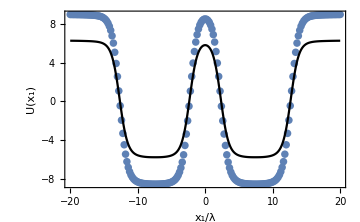

```mathematica
Show[pSum,pCont,ImageSize->Medium]
```

```mathematica
SEMTabSkyrmion=IntTabSkyrmion+ParallelTable[{0,SEMOpEvaluatedSkyrmionEpsilon[x,0,λMeso,1]},{x,-100,100,1/5}];
```

```mathematica
pSEM=ListLinePlot[SEMTabSkyrmion,PlotStyle->Red,AxesLabel->{"x_1/λ","U(x_1)"},LabelStyle->{FontSize->15}];
```

Now we compare with the SEM expansion.

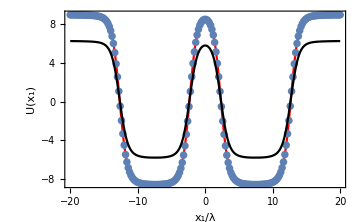

```mathematica
Show[pSEM,pSum,pCont,Frame->True,ImageSize->Medium]
```